```mathematica
SetDirectory[NotebookDirectory[]];
<< Italy2018ElectionDataAnalysis.wl;
```

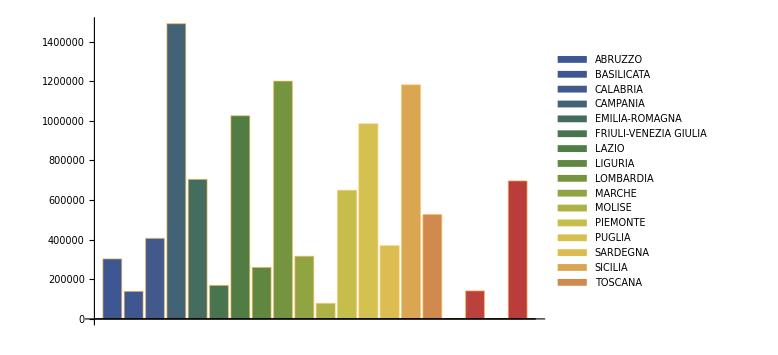

```mathematica
BarChart[PlottingElectionRegionCoalitionsBars["camera", "Centro"], ChartLegends->GetRegions[], ImageSize->Large, ChartStyle->"DarkRainbow"]
```

```mathematica
PieChart[PlottingElectionEloctorsPie["camera", Null, Null, Null, Null], ChartLegends->{"Elettori maschi", "Elettori femmine"}]
```

-Graphics-

```mathematica
PieChart[PlottingElectionVotersPie["camera", Null, Null, Null, "ELETTORI = 13746"], ChartLegends->{"Votanti maschi", "Votanti femmine"}]
```

-Graphics-

```mathematica
PieChart[PlottingElectionVotersNonVotersPie["camera", Null, Null, Null, "ELETTORI = 13746"], ChartLegends->{"Votanti maschi", "Votanti femmine", "Non votanti maschi", "Non votanti femmine"}]
```

-Graphics-